Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

April 14, 2021

To: Chief Scientist, Vertextin Inc.
From: Aakriti Lakshmanan
Subj: Case Study: Flucytosine PK Model

## Summary and Introduction

### Abstract:

As requested in the Scope of Work of March 23, 2017, we constructed a pharmacokinetic model in order to simulate renal failure and its effects on the drug concentration of Flucytosine.

### Introduction/Background Information:

In the following tech memo, we will be developing a PKPB model for an individual with a Candida Albicans overgrowth. Candida Albicans is a form of fungal infection, and is actually the most common fungal infection in the modern world. Candida Albicans that is present naturally in our body, including in the GI tract and in the mouth. However, it is sometimes possible for an overgrowth to occur which can also lead to infections. In fact, urinary tract infections are commonly caused by the Candida species of yeast. Some of the symptoms that are shown when you have an overgrowth or infection include rash and irritation. 

This is usually treated with a anti fungal pill, cream or suppository. However, another treatment would be an oral medication such as Flucytosine. [1] Flucytosine is commonly used with amphotericin B for more severe Candida infections. It was first created in 1957, and can cost up to 2k per day in the US. Some side effects of this drug are loss of appetite, diarrhea, and vomiting. In the case of an overdose, hydration and hemodialysis is very important. Specifically, hemodialysis, which is the external purification of the blood, is used when patients experience renal failure. [2]

Renal failure is a term that stands for kidney failure. Specifically, this refers to when the kidneys are working at less than 15% of the regular levels. There are two separate types: acute kidney failure, which occurs very quickly and can go away, as well as chronic kidney failure, which occurs slowly and is often permanent. Kidney failure occurs in around 3 out of 1000 individuals every year in the US. Scientists have highlighted the fact that there may be a genetic predisposition to the prevalence of kidney failure, specifically shown in the APOL1 gene for individuals of African origin. [3]

The kidney is very important for excretion and filtration of drug compounds. One of the processes involved in this is glomerular filtration, which is the first step in producing urine. The kidney filters out water-soluble waste products that enter the kidney through the blood, and sends it out of the body through the urine. Therefore, when renal failure occurs, the kidney is no longer able to function properly which means that drug are not excreted properly as well. [4]

## Methodology

For this study,  the following analyses were conducted:

A PBPK model was built in Stella

Using the model, the optimal dosage regimen for a 70 kg individual was determined

Renal Failure was simulated at different levels to understand its impact on the individual/drug concentration in the plasma and other regions.

A drug profile was built for Flucytosine.

## Results

### Drug Profile

A drug profile was built for Flucytosine, including information such as the number of rotatable bonds and the logP value. This data can be found in the table below.

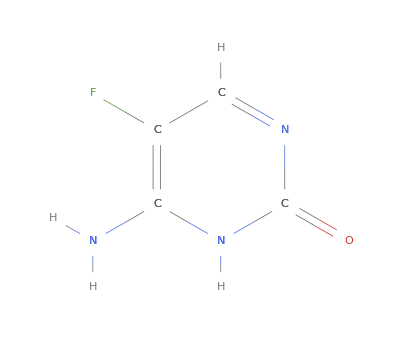
Formula | C_4H_4FN_3O
IUPAC Name | 4-amino-5-fluoro-3H-pyrimidin-2-one
Structural Formula | -Graphics-
Percent composition | {{C,37.22},{F,14.72},{H,3.12},{N,32.55},{O,12.39}}
Molecular Weight (g/mol) | 129.1 u
Density (g/mL) | Missing[NotAvailable]
Number of rotatable bonds | 0
logP | -1.1
TPSA | 67.5 Å^2
Hydrogen donors | 2
Hydrogen acceptors | 3
SMILES formula | C1=NC(=O)NC(=C1F)N
Classification of compound | {drugs,fluorinated compounds,halogenated compounds,organic compounds,solid compounds,heterocyclic compounds}

```mathematica
Grid[{{"Formula", ChemicalData["Flucytosine","Formula"]}, {"IUPAC Name", ChemicalData["Flucytosine","IUPACName"]}, {"Structural Formula", ChemicalData["Flucytosine","CHColorStructureDiagram"]}, {"Percent composition", ChemicalData["Flucytosine","ElementMassFraction"]}, {"Molecular Weight (g/mol)", ChemicalData["Flucytosine","MolecularWeight"]}, {"Density (g/mL)", ChemicalData["Flucytosine", "Density"]}, {"Number of rotatable bonds", ChemicalData["Flucytosine","RotatableBondCount"]}, {"logP", ChemicalData["Flucytosine", "PartitionCoefficient"]}, {"TPSA", ChemicalData["Flucytosine","TopologicalPolarSurfaceArea"]}, {"Hydrogen donors", ChemicalData["Flucytosine","HBondDonorCount"]}, {"Hydrogen acceptors", ChemicalData["Flucytosine","HBondAcceptorCount"]}, {"SMILES formula", ChemicalData["Flucytosine","SMILES"]}, {"Classification of compound", ChemicalData["Flucytosine","Memberships"]}}, Frame -> All]
```

### Dosing Regimens

Considering the ED50 and LD50 values are 0.1 mg/L and 0.05 mg/L respectively, it can be assumed that the dosage regimen must lead to a drug concentration that optimally fluctuates in between these values. Given that the individual weighs 70 kg, the optimal dosage regimen as seen in the model would be 75 mg of the drug with an interval of three hours. The calculated half-life of the drug with no renal failure is 3.51 hours. Half life is the amount of time needed for an amount (specifically drug concentration) to reduce to half the original value. Given this dosage regimen, the drug concentration can be visualized in the figure below:

If it is not possible to get a pill size of 75 mg, values of 70 mg or 80 mg would also be permissible for this specific individual. A dosage of 70 mg leads to the following drug concentration over time:

On the other hand, a dosage of 80 mg leads to the  drug concentration over time shown in the below figure. For the remaining calculations, we will use the aforementioned dosage regimen of 75 mg of the drug with an interval of three hours.

### Renal Failure

Renal failure refers to the failure of the kidney. Since the kidney plays a large role in the excretion of drugs, it can be inferred that the failure of 1 or 2 kidneys could have drastic effects on the concentration of the drug within the body. In order to simulate kidney failure in this model, renal function is considered a variable in the filter rate. Renal failure can be simulated as a percentage - 0%, as seen in the above model, means that the kidneys are working normally while 100% means that both of the kidneys have completely failed. In the following figures, we have examined different extents of renal failure and their impact on the drug concentration of Flucytosine. The following is the drug concentration with 25% renal failure with the same dosage regimen as above:

As can be seen in the graph, when the 25% renal failure occurs, the drug concentration in the plasma, intracellular regions and the extracellular regions all jumps up. However, the intracellular and extracellular concnetrains are mostly below the LD50, which means that while the indivdual may feel adverse symptoms, it will not be fatal. The half life of the drug jumps to 4.34 hours.

The above graph shows 50% renal failure, which means one of the kidneys has completely failed. We see the same pattern as before, however, the drug concnetration now jumps higher and the intra/extracellular concentrations are above the LD50. This has the potential to become fatal. However, there are still some points in time where the plasma concentration is acceptable. The half-life of the drug is now 5.7 hours.

This graph represents 75% renal failure. In this simulation, the jump is even more significant and deadly since all concentrations have significantly surpassed the LD50. The half-life of the drug jumps even more to 8.29 hours.

This graph represents 100% renal failure, which means that both the kidneys have failed. This individual will most likely face death unless the failure is recognized early and the individual stops taking the drug. As can be seen in the graph, the concentrations are extremely high and toxic/lethal in all regions of the body. The half-life of the drug after 100% renal failure is 15.2 hours.

### Model Overview

The model used to calculate the above analyses can be found below.

Genez very much appreciates the opportunity to conduct this work and hopes that the results are satisfactory. We look forward to a long working relationship with Vertextin, and wish your company success in its scientific ventures.

I certify that this work was completed by me on April 14, 2021.  All references and resources are cited.  Assistance was provided by Mr. Gotwals.
  Electronic signature: -Graphics-

References:

1.	https://www.medicalnewstoday.com/articles/322722#other-infections
	2.	https://en.wikipedia.org/wiki/Flucytosine#Overdose
	3.	https://en.wikipedia.org/wiki/Kidney_failure
	4.	https://www.niddk.nih.gov/health-information/kidney-disease/kidneys-how-they-work